# Infinite 3D medium, Isotropic Point Source, Rayleigh Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointRayleighscatter`"]
```

inf3DisopointRayleighscatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

## Analytical solutions

### Fluence: exact solution

[Grosjean 1963 - A New Approximate One-Velocity Theory for Treating both Isotropic and Anisotropic Multiple Scattering Problems, p. 37]

```mathematica
ϕexact[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((9 u^2-3 u (6-3 c+2 u^2) ArcTan[u]+(9+6 u^2+9 u^4-3 c (3+u^2)) ArcTan[u]^2)/(u (-9 (-1+c) c u+3 c u^3+8 u^5+3 c (3 (-1+c)+(-2+c) u^2-3 u^4) ArcTan[u])))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕexact[r_,Σt_,c_,1]:=(c Σt)/(2 Pi^2 r)NIntegrate[u((9 u^2-6 u (3+u^2) ArcTan[u]+(9+6 u^2+9 u^4) ArcTan[u]^2)/(8 u^6))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕexact[r_,Σt_,c_,2]:=(c Σt)/(2 Pi^2 r)NIntegrate[u(1/(64 u^11)3 (-9 u^3 (3+u^2)+(81 u^2+54 u^4+57 u^6) ArcTan[u]-u (81+81 u^2+123 u^4+35 u^6) ArcTan[u]^2+3 (3+2 u^2+3 u^4)^2 ArcTan[u]^3) c)Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

```mathematica
ϕexact[r_,Σt_,c_,3]:=(c Σt)/(2 Pi^2 r)NIntegrate[u(1/(512 u^16)9 (27 u^4 (3+2 u^2+3 u^4)-12 u^3 (27+27 u^2+45 u^4+13 u^6) ArcTan[u]+6 u^2 (81+108 u^2+198 u^4+108 u^6+49 u^8) ArcTan[u]^2-4 u (81+135 u^2+270 u^4+210 u^6+161 u^8+39 u^10) ArcTan[u]^3+3 (3+2 u^2+3 u^4)^3 ArcTan[u]^4) c^2)Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

### Rigorous asymptotic diffusion

```mathematica
Clear[c,b,g,x,v];
grosjeanΔ=buildΔ4[3]/.A[0]->1/.A[1]->0/.A[2]->1/2;
dgrosjeanΔ=D[grosjeanΔ/.u->I v,c];
xpsolve=Solve[D[grosjeanΔ==0/.u->I x[c],c],x'[c]][[1,1,-1]];
grosjeang=buildg4[3]/.A[0]->1/.A[1]->0/.A[2]->1/2/.u->I v;
```

```mathematica
(grosjeang(xpsolve x[c] 2/.x[c]->v))/dgrosjeanΔ/.Solve[grosjeanΔ==0/.u->I v,ArcTanh[v]]//FullSimplify
```

{-(32 v^6 (-1+v^2))/(9 c ((-10+c) (-1+c)^2+2 (-1+c) (-7+4 c) v^2+(-6+5 c) v^4+2 v^6))}

```mathematica
grosjeanΔ/.u->I V
```

1+(9 c)/(8 V^4)-(9 c^2)/(8 V^4)-(3 c)/(8 V^2)-(9 c ArcTanh[V])/(8 V^5)+(9 c^2 ArcTanh[V])/(8 V^5)+(3 c ArcTanh[V])/(4 V^3)-(3 c^2 ArcTanh[V])/(8 V^3)-(9 c ArcTanh[V])/(8 V)

```mathematica
rayleighv0inv[c_]:=ReplaceAll[Abs[V],FindRoot[1+(9 c)/(8 V^4)-(9 c^2)/(8 V^4)-(3 c)/(8 V^2)-(9 c ArcTanh[V])/(8 V^5)+(9 c^2 ArcTanh[V])/(8 V^5)+(3 c ArcTanh[V])/(4 V^3)-(3 c^2 ArcTanh[V])/(8 V^3)-(9 c ArcTanh[V])/(8 V),{V,0.8}]];
```

```mathematica
ϕrigourousDiffusion[r_,Σt_,c_]:=Σt/(4 Pi r)(-(32 #1^6 (-1+#1^2))/(9 c ((-10+c) (-1+c)^2+2 (-1+c) (-7+4 c) #1^2+(-6+5 c) #1^4+2 #1^6)))Exp[-# r Σt]&[rayleighv0inv[c]]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_rayleighscatter*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,13]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
numcollorders=simulations[[1]][[3]][[2,13]];
maxr=simulations[[1]][[3]][[2,5]];dr=simulations[[1]][[3]][[2,7]];
numr=Floor[maxr/dr];
```

## Compare MC and deterministic

### Mean Track Length

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[-1]];
meanTL=data[[-1]]
mfp/(1-c)
```

{Mean,track,length:,5.00103}

5.

### Fluence - Exact solution comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

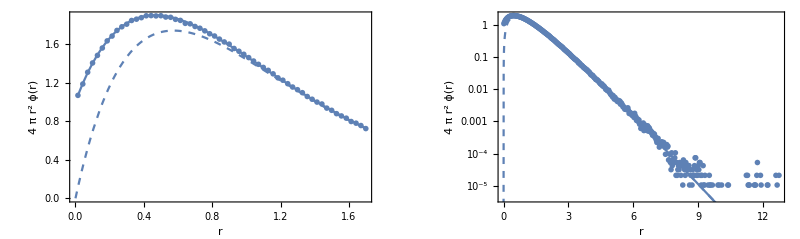

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[-1]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Plot[4 Pi r^2 ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotStyle->Dashed,PlotRange->All],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
LogPlot[4 Pi r^2 ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotStyle->Dashed],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (continuous) and Rigorous Asymptotic Diffusion (dashed)\nInfinite 3D, isotropic point source, Rayleigh scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### N-th collided Fluence - Exact solution comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

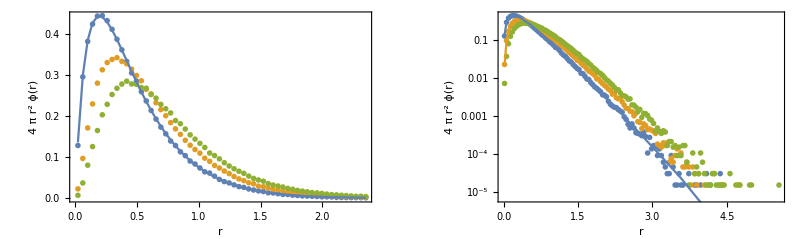

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluencei1=3 numcollorders+15+1;
fluencei2=3 numcollorders+15+2;
fluencei3=3 numcollorders+15+3;

pointsFluence1=ppoints[data[[fluencei1]],dr,maxr];
pointsFluence2=ppoints[data[[fluencei2]],dr,maxr];
pointsFluence3=ppoints[data[[fluencei3]],dr,maxr];
exact1Fluence1Shallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,1]}]& /@pointsFluence1[[1;;60]];
exact1Fluence1=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,1]}]& /@pointsFluence[[61;;-1;;10]];
exact1Fluence2Shallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,2]}]& /@pointsFluence1[[1;;60]];
exact1Fluence2=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,2]}]& /@pointsFluence[[61;;-1;;10]];
exact1Fluence3Shallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,3]}]& /@pointsFluence1[[1;;60]];
exact1Fluence3=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,3]}]& /@pointsFluence[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[{pointsFluence1[[1;;60]],pointsFluence2[[1;;60]],pointsFluence3[[1;;60]]},PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[{exact1Fluence1Shallow,exact1Fluence2Shallow,exact1Fluence3Shallow},PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[{pointsFluence1,pointsFluence2,pointsFluence3},PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[{exact1Fluence1Shallow,exact1Fluence2Shallow,exact1Fluence3Shallow},PlotRange->All,Joined->True],
ListLogPlot[{exact1Fluence1,exact1Fluence2,exact1Fluence3},PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (Fourier)\nInfinite 3D medium, isotropic point source, Rayleigh scattering, n-th scattered fluence ϕ[r|"<>ToString[collisionOrder]<>"], c ="<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

#### mfp 1

```mathematica
mfp=1;
sims1=Select[simulations,#[[2]]==mfp&];
```

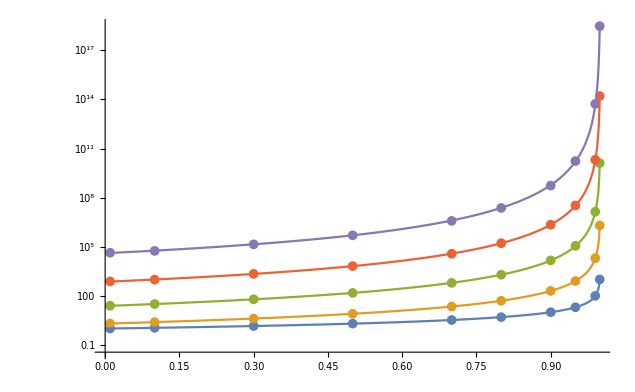

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),(2 mfp^3)/(-1+c)^2,-(120 (-2+c) mfp^5)/((-10+c) (-1+c)^3),(720 (100+c (-116+37 c)) mfp^7)/((-10+c)^2 (-1+c)^4),(5760 (49000+c (-93580+c (64230+c (-15937+256 c)))) mfp^9)/(7 (-10+c)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```

#### mfp 0.3

```mathematica
mfp=0.3;
sims1=Select[simulations,#[[2]]==mfp&];
```

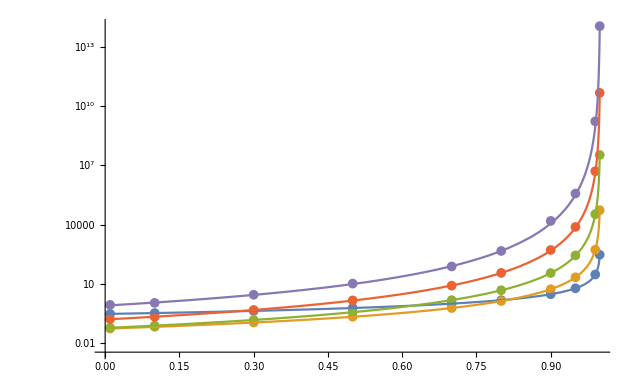

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),(2 mfp^3)/(-1+c)^2,-(120 (-2+c) mfp^5)/((-10+c) (-1+c)^3),(720 (100+c (-116+37 c)) mfp^7)/((-10+c)^2 (-1+c)^4),(5760 (49000+c (-93580+c (64230+c (-15937+256 c)))) mfp^9)/(7 (-10+c)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```